# Discos duros

## Inicialización del sistema

Definiciones básicas de las propiedades del sistema a simular

```mathematica
InitializeSystem[diameter_,lengthx_,lengthy_]:=(
{xl,yl} = {lengthx, lengthy};
σ = diameter;
box = Rectangle[{0,0},{xl,yl}];
);
```

Generar los discos dentro de la caja

```mathematica
GenerateDisks[n_]:=Block[{radius,region,diskArray,disk},
radius = σ/2;
(* Se crea la región para colocar los discos *)
region = Rectangle[{radius,radius},{xl-radius,yl-radius}];
diskArray = Table[
(* Verificamos si hay espacio disponible para poner un disco nuevo *)
If[!RegionEqual[region,EmptyRegion[2]],
(* Creamos una región del disco con coordenada aleatoria *)
disk = Disk[RandomPoint[region],radius];
(* Eliminar el área correspondiente al disco que acabamos de crear *)
region = RegionDifference[region,Replace[disk,h_[a_,b_]:>h[a,2 b]]];
(* Retornar el disco completo *)
<|"Position"->First[disk],"Velocity"->RandomReal[{-1,1},2],"Mass"->1|>
,
Nothing
]
,
n
];
Return[diskArray];
];
```

```mathematica
InitializeSystem[1,10,10]
```

```mathematica
diskList = GenerateDisks[10]
```

{<|Position→{1.12063,7.79627},Velocity→{0.529765,0.00851151},Mass→1|>,<|Position→{7.62665,1.98378},Velocity→{0.60021,-0.0147455},Mass→1|>,<|Position→{2.98113,6.07019},Velocity→{-0.27999,-0.951569},Mass→1|>,<|Position→{6.85098,8.08444},Velocity→{-0.455755,-0.860486},Mass→1|>,<|Position→{3.84949,8.90477},Velocity→{0.593941,0.883109},Mass→1|>,<|Position→{1.6997,9.33637},Velocity→{0.727705,-0.812274},Mass→1|>,<|Position→{2.5774,8.63755},Velocity→{-0.757997,-0.280791},Mass→1|>,<|Position→{1.82095,4.00354},Velocity→{0.973584,-0.126665},Mass→1|>,<|Position→{5.7929,8.38264},Velocity→{-0.239137,-0.00580303},Mass→1|>,<|Position→{8.23665,0.721583},Velocity→{0.616639,0.830594},Mass→1|>}

Representación visual del sistema

```mathematica
PlotDisks[disks_]:=Block[{diskRegions,arrows,labels,plot},
diskRegions = Map[Disk[#,σ/2]&,disks[[All,"Position"]]];
arrows = Map[Arrow[{#["Position"],#["Position"]+#["Velocity"]}]&,disks];
labels = Table[Text[ToString[i],disks[[i,"Position"]]+{0.0,0.2}],{i,1,Length[disks]}];
plot = Graphics[
{
EdgeForm[Thick],White,box,
EdgeForm[Thick],White,diskRegions,
Dashed,Red,arrows,
Black, labels
},
PlotRange->{{-1,1+xl},{-1,yl+1}}
];
Return[plot];
];
```

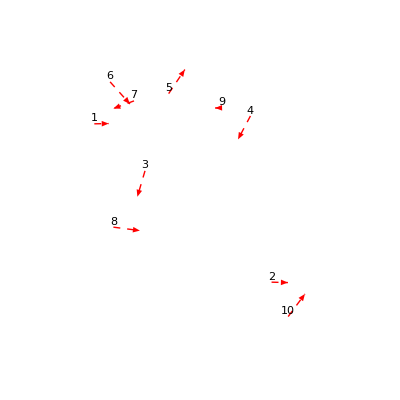

```mathematica
PlotDisks[diskList]
```

## Detección de colisiones

## Colisiones entre discos

### Texto: Reporte “Discos Duros” de Gilberto Aguilar Pérez y Gabriela Villegas Sánchez. Cómputo científico, Octubre de 2016.

El tiempo de colisión (corregido) es:

t_c = (- Δ(r⃗)_ij ·Δ(v⃗)_ij±√((Δ(r⃗)_ij ·Δ(v⃗)_ij)^2-(Δ(v⃗)_ij)^2((Δ(r⃗)_ij)^2-σ^2)))/(Δ(v⃗)_ij)^2

```mathematica
MinimumPositive[l_]:=Min[Select[l,Positive]];
CollisionTimeDisk[disks_,i_,j_]:=Block[{Δr,Δv,b,discriminant,tc},
Δr = disks[[i,"Position"]]-disks[[j,"Position"]];
Δv = disks[[i,"Velocity"]]-disks[[j,"Velocity"]];
b = Δr.Δv;
If[b>0,Return[Nothing]];

discriminant = b^2-Δv.Δv(Δr.Δr-σ^2);
If[discriminant>0,
tc = MinimumPositive[{(-b+√discriminant)/(Δv.Δv),(-b-√discriminant)/(Δv.Δv)}];
If[tc==∞,
Return[Nothing],
Return[<|"ParticleI"->i,"ParticleJ"->j, "CollisionTime"->tc|>]
];
,
Return[Nothing];
];
];
```

```mathematica
MinimumPositive[{-4,-3}]
```

∞

## Colisiones contra la pared

```mathematica
Cuadrant[v_]:=Which[
First[v]≥0 && Last[v]≥0, 1,
First[v]<0 && Last[v]≥0, 2,
First[v]<0 && Last[v]<0, 3,
First[v]≥0 && Last[v]<0, 4
];
WallFinder[walls_,ts_]:=Block[{transposed,clean,selectedWall,timeOfCollision},
transposed = Transpose[{walls,ts}];
clean = DeleteCases[transposed,{_,x_}/;x<0];
{selectedWall,timeOfCollision} = First[MinimalBy[clean,Last]];

Return[<|"Wall"->selectedWall,"CollisionTime"->timeOfCollision|>];
];
CollisionTimeWall[disks_,i_]:=Block[{diskR,diskVR,cuadrant,radius,wallAndT},
diskR = disks[[i,"Position"]];
diskVR = disks[[i,"Velocity"]];
cuadrant = Cuadrant[diskVR];
radius = σ/2;
wallAndT = Switch[cuadrant,
1,WallFinder[{1,4},{(xl-radius-First[diskR])/First[diskVR],(yl-radius-Last[diskR])/Last[diskVR]}],
2,WallFinder[{3,4},{(0.0+radius-First[diskR])/First[diskVR], (yl-radius-Last[diskR])/Last[diskVR]}],
3,WallFinder[{2,3},{(0.0+radius-Last[diskR])/Last[diskVR],(0.0+radius-First[diskR])/First[diskVR]}],
4,WallFinder[{1,2},{(xl-radius-First[diskR])/First[diskVR],(0.0+radius-Last[diskR])/Last[diskVR]}]
];
Return[Prepend[wallAndT,"ParticleI"->i]];
];
```

## Algoritmo principal

```mathematica
UpdatePosition[disk_,t_]:=Block[{newPosition},
newPosition = disk["Position"]+disk["Velocity"]*t;
<|"Position"->newPosition, "Velocity"->disk["Velocity"], "Mass"->disk["Mass"]|>
];
UpdatePositions[disks_,t_]:=Map[UpdatePosition[#,t]&,disks];

UpdateWallVelocity[disks_, collision_]:=Block[{diskI},
diskI = Part[disks,collision["ParticleI"]];
diskI["Velocity"] *= Switch[collision["Wall"],
1,{-1,1},
2,{1,-1},
3,{-1,1},
4,{1,-1}
];

Return[ReplacePart[disks,collision["ParticleI"]->diskI]];
];

UpdateDiskVelocity[disks_, collision_]:=Block[{diskI,diskJ,r,vr,b},
{diskI,diskJ} = Part[disks,{collision["ParticleI"],collision["ParticleJ"]}];
r = diskI["Position"]-diskJ["Position"];
vr = diskI["Velocity"]-diskJ["Velocity"];
b = r.vr;

diskI["Velocity"] -= (2 * diskJ["Mass"]*b*r)/(σ^2(diskI["Mass"]+diskJ["Mass"]));

diskJ["Velocity"] += (2 * diskI["Mass"]*b*r)/(σ^2(diskI["Mass"]+diskJ["Mass"]));

Return[ReplacePart[disks,{collision["ParticleI"]->diskI,collision["ParticleJ"]->diskJ}]];
];
```

```mathematica
UpdateAll[disks_]:=Block[{diskCollisionTable,nextDiskCollision,wallsCollisionTime,nextWallCollision,updPos},
(* Cálculo de los tiempos de colisión con otros discos *)
diskCollisionTable = Flatten[Table[CollisionTimeDisk[disks,i,j],{i,1,Length[disks]},{j,i+1,Length[disks]}]];
If[Length[diskCollisionTable]>0,
nextDiskCollision = First[MinimalBy[diskCollisionTable,Key["CollisionTime"]]],
nextDiskCollision = <|"CollisionTime"->∞|>
];

(* C+alculo del tiempo de colisión con la pared*)
wallsCollisionTime = Table[CollisionTimeWall[disks,i],{i,1,Length[disks]}];
nextWallCollision = First[MinimalBy[wallsCollisionTime,Key["CollisionTime"]]];

If[nextDiskCollision["CollisionTime"]>nextWallCollision["CollisionTime"],
updPos = UpdatePositions[disks, nextWallCollision["CollisionTime"]];
Return[UpdateWallVelocity[updPos, nextWallCollision]];
,
updPos = UpdatePositions[disks, nextDiskCollision["CollisionTime"]];
Return[UpdateDiskVelocity[updPos, nextDiskCollision]];
]
];
```

## Experimentos

### Simulación

Damos valores iniciales al sistema.

```mathematica
InitializeSystem[1,10,10];
```

Generar 20 discos con posiciones y velocidades aleatorias.

```mathematica
disks = GenerateDisks[20];
```

Cálculo de la dinámica.

```mathematica
dynamic = NestList[UpdateAll,disks,10000];
```

Gráfica

```mathematica
plts = Map[PlotDisks,dynamic];
```

```mathematica
Manipulate[plts[[i]],{i,1,Length[plts],1}]
```

### Mediciones

Definición de la norma de la velocidad y la energía total

```mathematica
VelocitiesNorm[disks_]:=Map[Norm[#["Velocity"]]&,disks];
Energies[disks_]:=Block[{velocities},
velocities = VelocitiesNorm[disks];
Map[1/2#^2&,velocities]
];
TotalEnergy[disks_]:=Total[Energies[disks]];
```

```mathematica
energies = Map[Energies,dynamic];
```

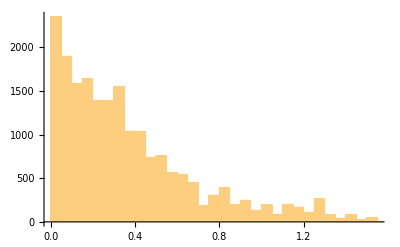

```mathematica
Histogram[Flatten[energies]]
```

```mathematica
velocities = Map[VelocitiesNorm,dynamic];
```

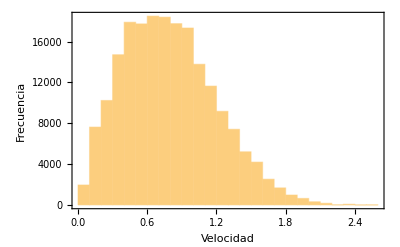

```mathematica
Histogram[
Flatten[velocities],
Frame->True,
FrameLabel->{"Velocidad","Frecuencia"}
]
```